## Isaac Lewis 4/24/24 M2 Free Fall with and without drag

```mathematica
Quit
```

```mathematica
sol= DSolve[{m*x''[t]==-m*g, x[0]==x0,x'[0]==v0},x[t],t];
x[t] = sol[[1]][[1]][[2]]
```

Position  Free  fall  equation no drag

1/2 (-g t^2+2 t v0+2 x0)

```mathematica
x'[t] = D[x[t],t]
```

Velocity  free  fall  equation no drag

1/2 (-2 g t+2 v0)

```mathematica
x''[t]=D[x'[t],t]
```

Acceleration  free  fall  no  drag

-g

```mathematica
m = 3;
g= 9.8;
x0 = 0;
v0 = 10;
x[t]
```

1/2 (20 t-9.8 t^2)

Had  to  copy  and  paste  value  of  x[t]  into  plot; discussed  in  office  hours  4/24/24

Position  Plot Free  Fall No Drag

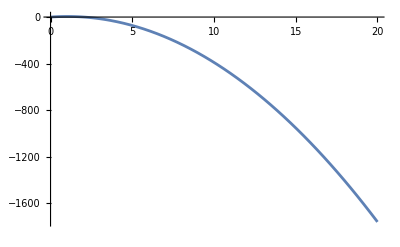

```mathematica
Plot[1/2 (20 t-9.8 t^2),{t,0,20}]
```

Velocity  Plot    Free  Fall No Drag

```mathematica
m = 3;
g= 9.8;
x0 = 0;
v0 = 10;
```

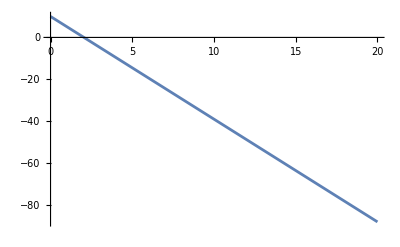

```mathematica
Plot[-1/2  g t+ v0,{t,0,20}]
```

Acceleration  Plot  Free  Fall  No  Drag

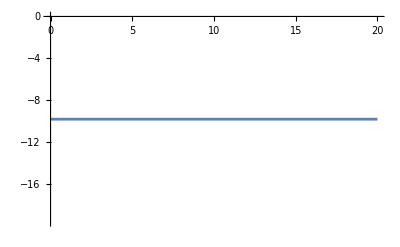

```mathematica
m = 3;
g= 9.8;
x0 = 0;
v0 = 10;
Plot[-g,{t,0,20}]
```

```mathematica
Clear[m,g,x0,v0]
```

Position  with  drag

```mathematica
soldrag = DSolve[{m*x''[td]==-m*g-b*x'[td], x[0]==x00,x'[0]==V},x[td],td];
x[td] = soldrag[[1]][[1]][[2]]
```

(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/b^2

Velocity  with  drag

```mathematica
x'[td] = D[x[td],td]
```

-(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/(b m)+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/b^2

Acceleration  with  drag

```mathematica
x''[td] = D[x'[td],td]
```

(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/m^2+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g-(b^3 ⅇ^((b td)/m) g td)/m+(b^3 ⅇ^((b td)/m) V)/m+(b^4 ⅇ^((b td)/m) x00)/m^2))/b^2-(2 ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/(b m)

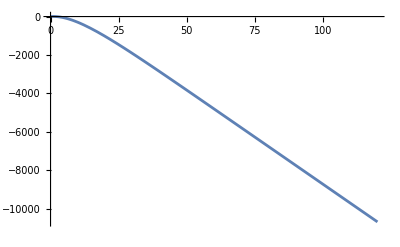

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Plot[(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/b^2,{td,0,120}]
```

Velocity  Plot with drag

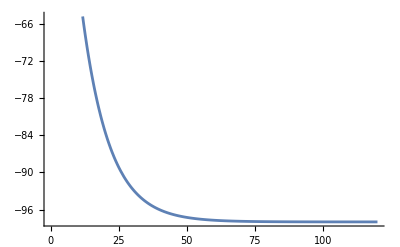

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Plot[-(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/(b m)+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/b^2,{td,0,120}]
```

Acceleration  Plot with drag

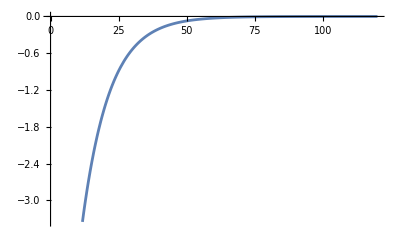

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Plot[(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/m^2+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g-(b^3 ⅇ^((b td)/m) g td)/m+(b^3 ⅇ^((b td)/m) V)/m+(b^4 ⅇ^((b td)/m) x00)/m^2))/b^2-(2 ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/(b m),{td,0,120}]
```

Position with drag  Plot  With  Sliders

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Manipulate[Plot[(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/b^2,{td,0,120}],{{m,1},1,10},{{V,1},-10,20},{{b,0.1},0,1}]
```

Velocity with drag  Plot  with  sliders

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Manipulate[Plot[-(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/(b m)+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/b^2,{td,0,120}],{{m,1},1,10},{{V,1},-10,20},{{b,0.1},0,1}]
```

Acceleration with drag  Plot  with  Sliders

```mathematica
m = 1;
g= 9.8;
x00 = 0;
V = 10;
b = 0.10;
Manipulate[Plot[(ⅇ^(-(b td)/m) (-g m^2+ⅇ^((b td)/m) g m^2-b ⅇ^((b td)/m) g m td-b m V+b ⅇ^((b td)/m) m V+b^2 ⅇ^((b td)/m) x00))/m^2+(ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g-(b^3 ⅇ^((b td)/m) g td)/m+(b^3 ⅇ^((b td)/m) V)/m+(b^4 ⅇ^((b td)/m) x00)/m^2))/b^2-(2 ⅇ^(-(b td)/m) (-b^2 ⅇ^((b td)/m) g td+b^2 ⅇ^((b td)/m) V+(b^3 ⅇ^((b td)/m) x00)/m))/(b m),{td,0,120}],{{m,1},1,10},{{V,1},-10,20},{{b,0.1},0,1}]
```

```mathematica
Clear[m,g,x00,V,b]
```